## Free trajectory phase

give kick wait until overlapped then interfere

```mathematica
x[t_]:=v0/ω Sin[ω t]
assum={v0∈Reals,m∈Reals,ω∈Reals,vk∈Reals,x0∈Reals,ω>0}
x[t]
x'[t]
```

{v0∈ℝ,m∈ℝ,ω∈ℝ,vk∈ℝ,x0∈ℝ,ω>0}

(v0 Sin[t ω])/ω

v0 Cos[t ω]

```mathematica
period = (2π)/ω;
Lagrangian [t_]:=Simplify[ 1/2 m (x'[t])^2- 1/2 m ω^2 (x[t])^2,Assumptions->assum]
Lagrangian[t]
```

1/2 m v0^2 Cos[2 t ω]

If we allow the oscillation until returning to the origin, the the phase is zero

```mathematica
action=Integrate[Lagrangian[t],{t,0,t1},Assumptions->assum]
```

(m v0^2 Sin[2 t1 ω])/(4 ω)

```mathematica
action/.t1->period
action/.t1->period/4
action/.t1->period/2
```

0

0

0

This is caused by the sign of the Lagrangian flipping

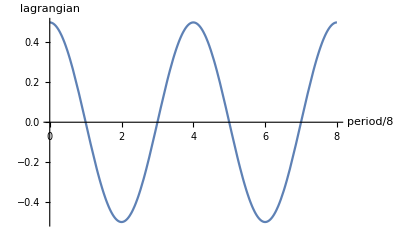

```mathematica
Plot[Lagrangian[t*period/8]/.{v0->1,m->1,ω->1},{t,0,8},AxesLabel->{"period/8","lagrangian"}]
```

```mathematica
ParametricPlot3D[{x[t],x'[t],Lagrangian[t]}/.{v0->1,m->1,ω->1},{t,0,period/.{v0->1,m->1,ω->1}},ColorFunction->Function[{x,y,u},Hue[u]]]
```

-Graphics3D-

```mathematica
action
```

(m v0^2 Sin[2 t1 ω])/(4 ω)

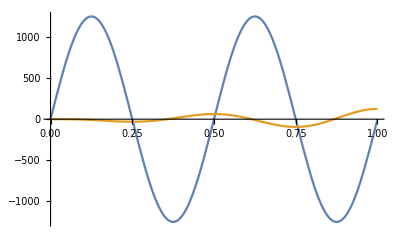

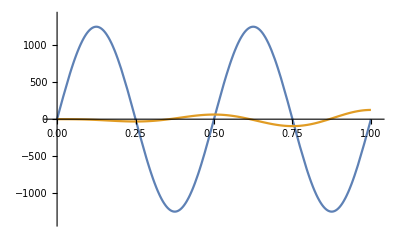

```mathematica
Plot[{{action/ℏ/.t1->period*n/.{ω->20*2π,v0->0.1,ℏ->1.0545718×10^-34,m->6.64648×10^-27}},
{D[action/ℏ,ω]/.t1->period*n/.{ω->20*2π,v0->0.1,ℏ->1.0545718×10^-34,m->6.64648×10^-27}}}
 ,{n,0,1}]
```

## Double kick phase

give kick wait t1 then mirror again

```mathematica
x[t_]:=v0/ω Sin[ω t]
```

```mathematica
Lagrangian[t]
```

1/2 m v0^2 Cos[2 t ω]

```mathematica
actiont1=Integrate[Lagrangian[t],{t,0,t1},Assumptions->assum]+Integrate[Lagrangian[t],{t,period/2 - t1,period/2 },Assumptions->assum]
actionPhase=actiont1/ℏ;
N[actiont1/.{p->1,m->1,ω->1}]
```

(m v0^2 Sin[2 t1 ω])/(2 ω)

0.5 v0^2 Sin[2. t1]

```mathematica
actiont1/.t1-> period/4
```

0

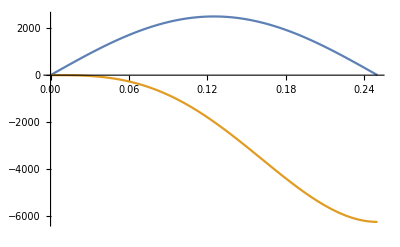

```mathematica
Plot[{{actionPhase/.{t1->n*period}/.{k->2π/ (1083 10^-9),ω->20*2π,v0->0.1,ℏ->1.0545718×10^-34,m->6.64648×10^-27}},
100*{D[actionPhase,ω]/.{t1->n*period}/.{k->2π/ (1083 10^-9),ω->20*2π,v0->0.1,ℏ->1.0545718×10^-34,m->6.64648×10^-27}}},{n,0,0.25}]
```

```mathematica
reflectionPos=x[t1]
```

(v0 Sin[t1 ω])/ω

```mathematica
reflectionPhase=reflectionPos*k
```

(k v0 Sin[t1 ω])/ω

```mathematica
actiont1/.t1->period/8
```

(m v0^2)/(2 ω)

```mathematica
reflectionPhase/.t1->period/8 /.{k->2π/ (1083 10^-9),ω->20*2π,v0->0.05}
```

1632.29

```mathematica
totalPhase=reflectionPhase+actionPhase
```

(k v0 Sin[t1 ω])/ω+(m v0^2 Sin[2 t1 ω])/(2 ω ℏ)

```mathematica
totalPhase/.{t1->period/8}
```

(k v0)/(√2 ω)+(m v0^2)/(2 ω ℏ)

```mathematica
D[totalPhase,ω]/.{t1->period/4}/.{k->2π/ (1083 10^-9),ω->20*2π,v0->0.1,ℏ->1.0545718×10^-34,m->6.64648×10^-27}
```

-99.4319

```mathematica
(k v0)/(√2)/.{k->2π/ (1083 10^-9),ω->10*2π,v0->0.01,ℏ->1.0545718×10^-34,m->6.64648×10^-27}
```

41023.8

```mathematica
(m v0^2)/(2  ℏ)/.{k->2π/ (1083 10^-9),ω->10*2π,v0->0.01,ℏ->1.0545718×10^-34,m->6.64648×10^-27}
```

3151.27

```mathematica
D[totalPhase,ω]
```

(k t1 v0 Cos[t1 ω])/ω+(m t1 v0^2 Cos[2 t1 ω])/(ω ℏ)-(k v0 Sin[t1 ω])/ω^2-(m v0^2 Sin[2 t1 ω])/(2 ω^2 ℏ)

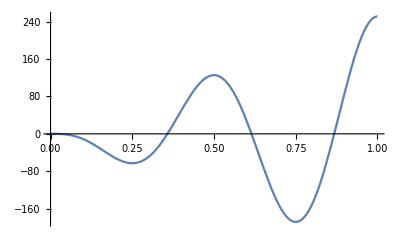

```mathematica
Plot[D[actionPhase,ω]/.{t1->n*period}/.{k->2π/ (1083 10^-9),ω->20*2π,v0->0.1,ℏ->1.0545718×10^-34,m->6.64648×10^-27},{n,0,1}]
```

## Arb inital vel and pos

```mathematica
HOwithArbStart=DSolve[{ x''[t] == -ω^2 x[t],x'[0]==v0,x[0]==x0},x[t],t]
HOwithArbStart=x[t]/.HOwithArbStart
HOwithArbStart=HOwithArbStart[[1]]
```

DSolve::dsfun: (v0 Sin[t ω])/ω cannot be used as a function.

DSolve[{True,True,0==x0},(v0 Sin[t ω])/ω,t]

ReplaceAll::reps: {DSolve[{True,True,0==x0},(v0 Sin[t ω])/ω,t]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

(v0 Sin[t ω])/ω/.DSolve[{True,True,0==x0},(v0 Sin[t ω])/ω,t]

(v0 Sin[t ω])/ω

If you use the identity for the sumation of cos and sin of the same freq
https://www.dsprelated.com/showarticle/635.php

```mathematica
x[t_]=√((x0)^2+(v0/ω)^2)Cos[ω t -ArcTan[v0/(x0 ω)]]
```

√(x0^2+v0^2/ω^2) Cos[t ω-ArcTan[v0/(x0 ω)]]

```mathematica
period = (2π)/ω;
Lagrangian [t_]:=Simplify[ 1/2 m (x'[t])^2- 1/2 m ω^2 (x[t])^2,Assumptions->assum]
```

```mathematica
ΔS=Integrate[Lagrangian[t],{t,0,period/2},Assumptions->assum]-Integrate[Lagrangian[t]/.{v0->v0+vk},{t,0,period},Assumptions->assum]
```

0

```mathematica
t1temp=period/8;
ΔS=Integrate[Lagrangian[t],{t,0,t1},Assumptions->assum] +
Integrate[Lagrangian[t],{t,period/2-t1,period/2},Assumptions->assum]-
Integrate[Lagrangian[t]/.{v0->v0+vb},{t,0,t1},Assumptions->assum]
FullSimplify[ΔS]
DelϕOpt=kopt*(x[0]-x[period/2]+x[t1])
```

-(m (v0^2+x0^2 ω^2) Cos[t1 ω-2 ArcTan[v0/(x0 ω)]] Sin[t1 ω])/(2 ω)-(m (v0^2+x0^2 ω^2) Cos[t1 ω+2 ArcTan[v0/(x0 ω)]] Sin[t1 ω])/(2 ω)+(m ((v0+vb)^2+x0^2 ω^2) Cos[t1 ω-2 ArcTan[(v0+vb)/(x0 ω)]] Sin[t1 ω])/(2 ω)

m (v0+vb) x0 Sin[t1 ω]^2-(m (-v0^2+2 v0 vb+vb^2+x0^2 ω^2) Sin[2 t1 ω])/(4 ω)

kopt ((2 √(x0^2+v0^2/ω^2))/(√(1+v0^2/(x0^2 ω^2)))+√(x0^2+v0^2/ω^2) Cos[t1 ω-ArcTan[v0/(x0 ω)]])